{{500.,1.×10^-43,0.005,{{0.5,0.},{0.894427,0.},{1.6,0.},{2.82843,0.},{5.,0.},{8.86002,0.},{15.7,0.},{28.0179,0.},{50.,0.},{88.8819,0.},{158.,0.}}},{3343.7,1.×10^-43,0.005,{{0.5,7.01115×10^-13},{0.894427,9.06494×10^-13},{1.6,8.85068×10^-13},{2.82843,5.06411×10^-13},{5.,0.},{8.86002,0.},{15.7,0.},{28.0179,0.},{50.,0.},{88.8819,0.},{158.,0.}}},{22360.7,1.×10^-43,0.005,{{0.5,1.33293×10^-13},{0.894427,2.48041×10^-13},{1.6,3.9764×10^-13},{2.82843,6.51433×10^-13},{5.,8.97841×10^-13},{8.86002,8.38582×10^-13},{15.7,7.41487×10^-13},{28.0179,0.},{50.,0.},{88.8819,0.},{158.,0.}}},{149535.,1.×10^-43,0.005,{{0.5,2.25942×10^-14},{0.894427,3.76579×10^-14},{1.6,6.62797×10^-14},{2.82843,1.15489×10^-13},{5.,2.11491×10^-13},{8.86002,3.42628×10^-13},{15.7,5.31201×10^-13},{28.0179,8.52124×10^-13},{50.,7.63942×10^-13},{88.8819,8.38966×10^-13},{158.,0.}}},{1.×10^6,1.×10^-43,0.005,{{0.5,3.72487×10^-15},{0.894427,6.83231×10^-15},{1.6,1.11832×10^-14},{2.82843,2.0369×10^-14},{5.,3.2744×10^-14},{8.86002,5.57604×10^-14},{15.7,9.91343×10^-14},{28.0179,1.66053×10^-13},{50.,2.99635×10^-13},{88.8819,4.52307×10^-13},{158.,7.444×10^-13}}}}

{{0.,0.,0.,0.,0.},{9.06494×10^-13,8.85068×10^-13,0.,0.,0.},{3.9764×10^-13,8.97841×10^-13,8.97841×10^-13,7.41487×10^-13,0.},{6.62797×10^-14,2.11491×10^-13,5.31201×10^-13,8.52124×10^-13,8.38966×10^-13},{1.11832×10^-14,3.2744×10^-14,9.91343×10^-14,2.99635×10^-13,7.444×10^-13}}

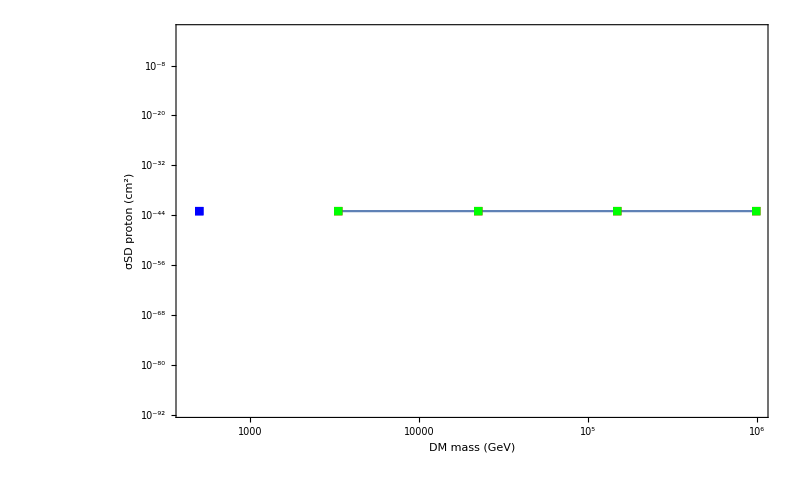

```mathematica
SetDirectory[NotebookDirectory[]];
tab=Import["efluxsingle.mx"];
tab
hawcbins={{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50,8.1 10^-14},{50,158,6.3 10^-14}};
sortpoints[table_]:=(
sortedtab=Table[{0.},{n,1,Length[tab]}];(*Initialising a final table to overwrite*)
Do[
sortedflux=hawcbins;
sortedfluxtab=hawcbins;
Do[sortedfluxtab⟦j⟧=Select[table⟦k,4⟧, hawcbins⟦j,1⟧≤#⟦1⟧≤hawcbins⟦j,2⟧&],{j,1,Length[hawcbins]}];
Do[sortedflux⟦j⟧=Max[Table[sortedfluxtab⟦j,i,2⟧,{i,1,Length[sortedfluxtab⟦j⟧]}]],{j,1,Length[hawcbins]}];
sortedtab⟦k⟧=sortedflux,
{k,1,Length[tab]}]
)(*sortpoints sorts all the eflux entries, by removing the masses and cross-sections, sorting the efluxes into bins that correspond to the hawc bins, and finding the max eflux in that bin -- so you end up with 5 entries per data point, each corresponding to the TeV cm^-2 s^-1 for that hawc bin*)
sortpoints[tab]
sortedtab
isexcluded[table_]:=Table[If[table[[i,1]]/1.>2.2 10^-12||table[[i,2]]/1.>8.8 10^-13||table[[i,3]]/1.>2.8 10^-13||table[[i,4]]/1.>8.1 10^-14||table[[i,5]]/1.>6.3 10^-14,1,0],{i,1,Length[tab]}]

exc=isexcluded[sortedtab];
(*inttab=Table[{{tab⟦i,1⟧,tab⟦i,2⟧},If[exc[[i]]==1,1,0]},{i,1,Length[tab]}];
intfunc=Interpolation[inttab];*)
exctab={};
allowedtab={};
Do[If[exc[[i]]==1,exctab=Append[exctab,{tab⟦i,1⟧,tab⟦i,2⟧}]],{i,1,Length[tab]}]
Do[If[exc[[i]]==0,allowedtab=Append[allowedtab,{tab⟦i,1⟧,tab⟦i,2⟧}]],{i,1,Length[tab]}]
masses=DeleteDuplicates[Table[exctab[[i,1]],{i,1,Length[exctab]}]];
minexc={};
Do[
minexc=Append[minexc,particularmass=Select[exctab,#[[1]]==masses[[i]]&][[1]]],{i,1,Length[masses]}];
excfunc=Interpolation[minexc,InterpolationOrder->1];
ListLogLogPlot[{exctab,allowedtab,minexc},PlotRange-> All,Frame-> True,FrameStyle-> Black,LabelStyle-> 15,ImageSize->800, FrameLabel->{"DM mass (GeV)","σSD proton (cm^2)"},PlotStyle->{Red,Blue,Green},PlotMarkers-> {"■","■","■"}];
Show[%,LogLogPlot[excfunc[mdm],{mdm,Min[masses],Max[masses]}]]
```

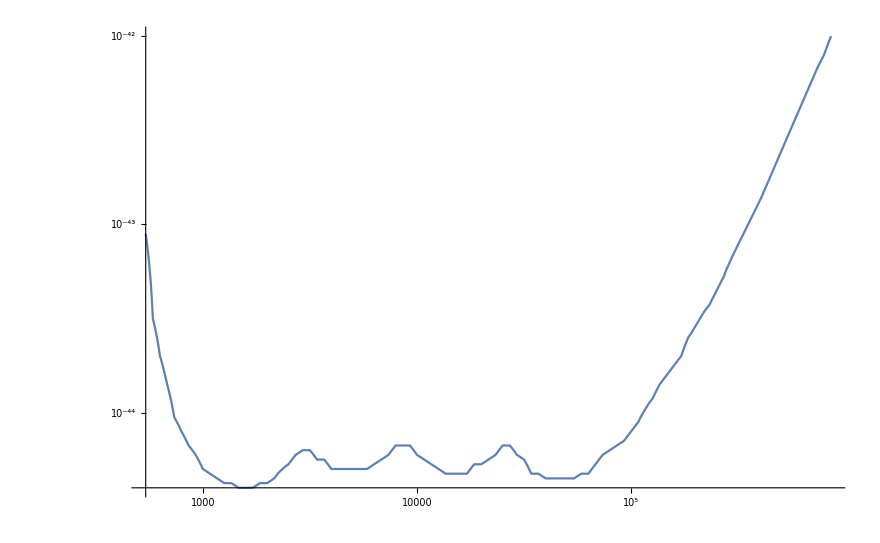

```mathematica
LogLogPlot[excfunc[mdm],{mdm,Min[masses],Max[masses]}]
```

```mathematica
tab
```

{{500.,3.16228×10^-46,{0.,0.,0.,0.,0.}},{500.,3.34965×10^-46,{0.,0.,0.,0.,0.}},6097,{100000.,1.×10^-44,{3.57766×10^-11,9.59234×10^-11,2.35726×10^-10,4.76383×10^-10,1.7643×10^-10}}}
 |  |  |  |